```mathematica
Remove["Global`*"]
H[a_,u_]=a/π Integrate[Exp[-y^2]/(a^2+(u-y)^2),{y,-∞,∞},Assumptions->{a∈Reals,u∈Reals,a≠0}]//PowerExpand //FullSimplify
```

1/2 ⅇ^((a-ⅈ u)^2) (Erfc[a-ⅈ u]+ⅇ^(4 ⅈ a u) Erfc[a+ⅈ u])

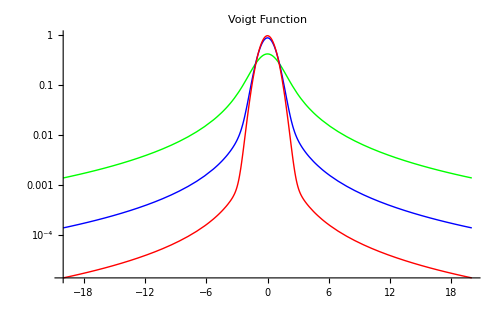

```mathematica
a0={1,0.1,0.01};
plots=Table[Abs[H[a,u]],{a,a0}];
LogPlot[plots,{u,-20,20},PlotStyle->Table[{Thick,Hue[i/3]},{i,1,3}],ImageSize->500,PlotRange->All,PlotLabel->"Voigt Function"]
```

```mathematica
τo=Table[10^(i),{i,-1.5,4.5,.5}];
τ[u_]=τo H[0.1,u]/H[0.1,0];
ρ:=Dimensions[τ[u]][[1]];
```

```mathematica
plots3=Table[Re[Exp[-τ[u][[i]]]],{i,1,ρ}];
Plot[plots3,{u,-20,20},PlotLegends->Table[-1.5+i,{i,0,6,.5}],PlotStyle->Table[{Thick,Hue[(1.5+Log10[τo[[i]]])/6]},{i,1,ρ}],ImageSize->Large,AxesOrigin->{-20,0},PlotRange->All,Exclusions->None,PlotLabel->"Voigt Absoption Line",AxesLabel->{"Iν/Iν_o","u"}]
```

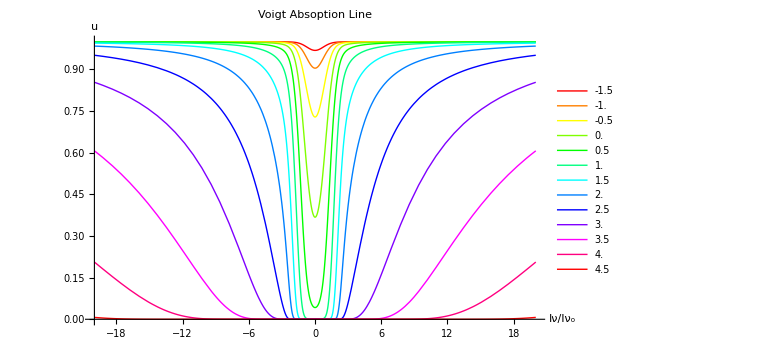

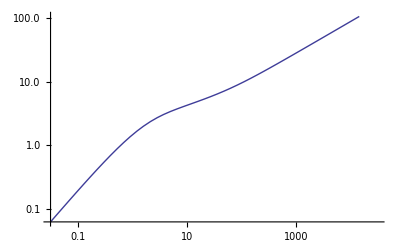

```mathematica
τp[u_]=t1 H[0.1,u]/H[0.1,0];
func=Re[1-Exp[-τp[u]]]//FullSimplify;
EW[t1_]:=NIntegrate[func,{u,-∞,∞}]
LogLogPlot[EW[t1],{t1,10^-1.5,10^4.5}]
```

```mathematica
Clear[A,B,Δν,a]
f=2^14/(3^9 2)//N;
h=6.626 10^-27;
m=9.109 10^-28 ;
q=4.803*^-10;
nu=2470*^12;
α=1/137;
c=2.99792458*10^10;

B=(2π α)/(nu m)f
A=2/8(% 2h nu^3)/c^2 
nuD=nu 30/c
a=A/(4π nuD)
```

8.4838×10^9

4.71261×10^8

2.47171×10^6

15.1724

```mathematica
ϕ[ν_]:=a/π Quiet[NIntegrate[Exp[-y^2]/(a^2+((ν-nu)/nuD-y)^2),{y,-∞,∞}]]
norm=Quiet[NIntegrate[ϕ[x],{x,.0,∞}]]
LogPlot[Quiet[ϕ[u]]/norm,{u,.85nu,1.15nu},PlotRange->All]
```

0.232215

NIntegrate::inumr: The integrand ⅇ^-y^2/230.201  + (4.04578×10^-7\ (-2470000000000000 + u) - y)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

-Graphics-

```mathematica
optic[n_]=(h nu)/(4π)n B 1/nuD √π ϕ[nu]
Exp[optic[10^5]]
(*LogPlot[1-Exp[-optic[n]],{n,1*^1,1*^15}]*)
```

2.93995×10^-10 n

1.00003

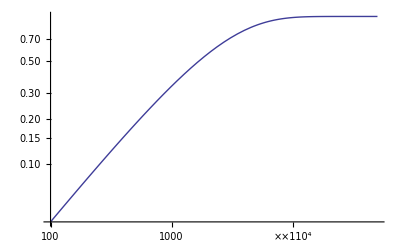

```mathematica
LogLogPlot[1-Exp[-.00041 x],{x,100,50000}]
```